```mathematica
SetDirectory[NotebookDirectory[]<>"..\\Main"]
Needs["SSS`"]
```

C:\Users\caviness\Documents\Git\SSS-Code\Main

### Generating & Displaying an SSS

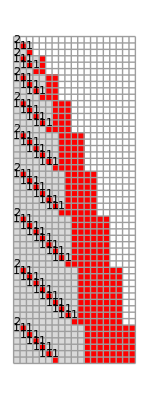


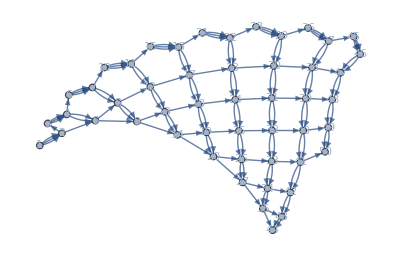
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
sss2D=SSS[{"ABA"->"AAB","A"->"ABA"},"A",50];
```

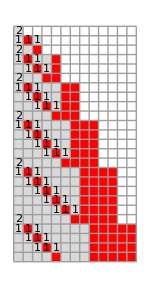
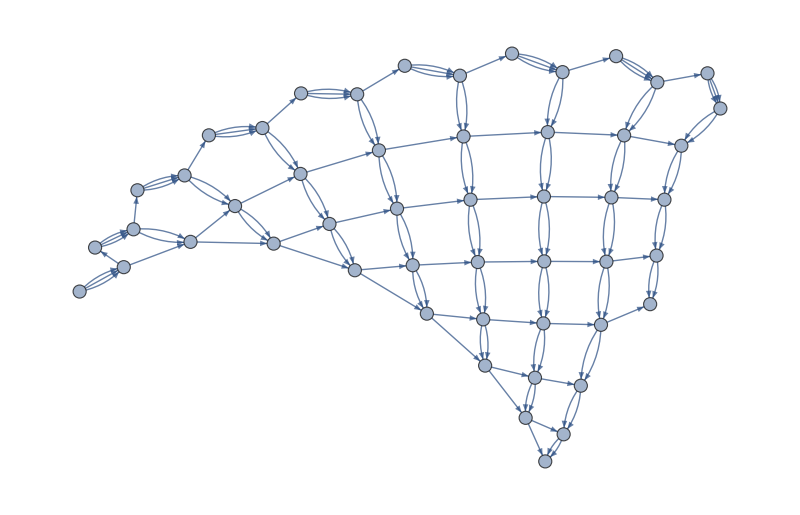
-Graphics-
-Graphics- | → | -Graphics-
-Graphics- | → | -Graphics-Substitution Rules:-Graphics-

```mathematica
SSSDisplay[sss2D, SSSMax->25,SSSSize->150,NetSize->800,VertexLabels->Placed["Name",Tooltip]]
```

#### A sub-heading (<alt+number>)

<ctrl-L> repeats Last input line:

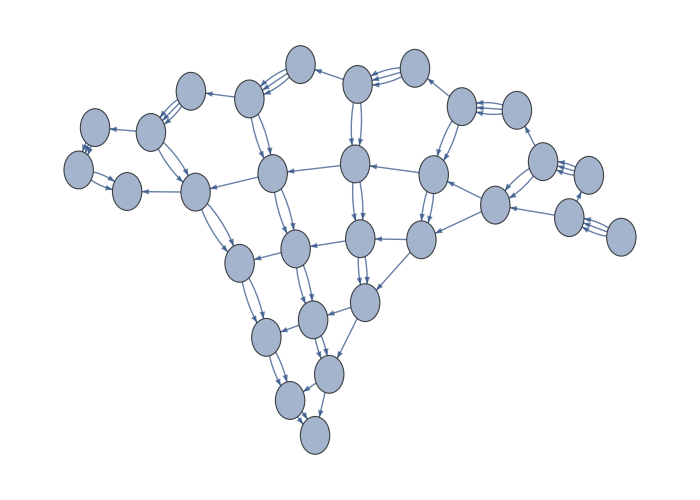

```mathematica
SSSDisplay[sss2D,SSSMax->25,SSSSize->{150,300},NetMax->30,NetSize->{700,500},NetMethod->{NoSSS,GraphPlot},VertexSize->0.8,VertexLabels->Placed["Name",Center]]
```

```mathematica
??SSSAnimate
```

```mathematica
SSSAnimate[sss2D,SSSMax->25,SSSSize->{150,300},NetMax->90,NetSize->{700,500},NetMethod->{NoSSS,GraphPlot},VertexSize->0.8,VertexLabels->Placed["VertexWeight",Center],DirectedEdges->True]
```

```mathematica
SSSInteractiveDisplay[sss2D]
```

```mathematica
Keys[sss2D]
```

{Net,OutDegreePotential,OutDegreeRemaining,OutDegreeActual,InDegree,ConnectionList,Verdict,RulesUsed,CellsDeleted,Distance,MaxColor,TagIndex,TEvolution,Evolution,RuleSet,TRuleSet,RuleSetWeight,RuleSetLength}

```mathematica
sss2D["Net"]
```

{1→2,1→2,1→2,2→3,3→4,3→4,3→4,4→5,4→5,2→5,4→6,6→7,6→7,6→7,7→8,7→8,5→8,8→9,8→9,5→9,7→10,10→11,10→11,10→11,11→12,11→12,8→12,12→13,12→13,9→13,13→14,13→14,9→14,11→15,15→16,15→16,15→16,16→17,16→17,12→17,17→18,17→18,13→18,18→19,18→19,14→19,19→20,19→20,14→20,16→21,21→22,21→22,21→22,22→23,22→23,17→23,23→24,23→24,18→24,24→25,24→25,19→25,25→26,25→26,20→26,26→27,26→27,20→27,22→28,28→29,28→29,28→29,29→30,29→30,23→30,30→31,30→31,24→31,31→32,31→32,25→32,32→33,32→33,26→33,33→34,33→34,27→34,34→35,34→35,27→35,29→36,36→37,36→37,36→37,37→38,37→38,30→38,38→39,38→39,31→39,39→40,39→40,32→40,40→41,40→41,33→41,41→42,41→42,34→42,42→43,42→43,35→43,43→44,43→44,35→44,37→45,45→46,45→46,45→46,46→47,46→47,38→47,47→48,47→48,39→48,48→49,48→49,40→49,49→50,49→50,41→50}

```mathematica
sss2D["RuleSet"]
```

{ABA→AAB,A→ABA}

```mathematica
sss2D["Evolution"]
```

{A,ABA,AAB,ABAAB,AABAB,AAABB,ABAAABB,AABAABB,AAABABB,AAAABBB,ABAAAABBB,AABAAABBB,AAABAABBB,AAAABABBB,AAAAABBBB,ABAAAAABBBB,AABAAAABBBB,AAABAAABBBB,AAAABAABBBB,AAAAABABBBB,AAAAAABBBBB,ABAAAAAABBBBB,AABAAAAABBBBB,AAABAAAABBBBB,AAAABAAABBBBB,AAAAABAABBBBB,AAAAAABABBBBB,AAAAAAABBBBBB,ABAAAAAAABBBBBB,AABAAAAAABBBBBB,AAABAAAAABBBBBB,AAAABAAAABBBBBB,AAAAABAAABBBBBB,AAAAAABAABBBBBB,AAAAAAABABBBBBB,AAAAAAAABBBBBBB,ABAAAAAAAABBBBBBB,AABAAAAAAABBBBBBB,AAABAAAAAABBBBBBB,AAAABAAAAABBBBBBB,AAAAABAAAABBBBBBB,AAAAAABAAABBBBBBB,AAAAAAABAABBBBBBB,AAAAAAAABABBBBBBB,AAAAAAAAABBBBBBBB,ABAAAAAAAAABBBBBBBB,AABAAAAAAAABBBBBBBB,AAABAAAAAAABBBBBBBB,AAAABAAAAAABBBBBBBB,AAAAABAAAAABBBBBBBB,AAAAAABAAAABBBBBBBB}

```mathematica
sss2D["Evolution"]⟦1⟧
```

A

```mathematica
sss2D⟦"Evolution"⟧⟦1⟧
```

A

```mathematica
sss2D⟦"Evolution",1⟧
```

A

```mathematica
l=Range[10,50,10]
```

{10,20,30,40,50}

```mathematica
l⟦2⟧
```

20

```mathematica
Head[sss2D]
```

Association

```mathematica
Head[l]
```

List

```mathematica
l⟦0⟧
```

List

```mathematica
TreeForm
```

```mathematica
a(2)
```

2 a